```mathematica
npop=30; (*number of nodes*)
ρ=0.24; (*prob of connection*)
```

```mathematica
adj=Table[If[i<=j,0,RandomVariate[BinomialDistribution[1,ρ]]],{i,1,npop},{j,1,npop}];
Table[If[i<j, adj[[i,j]]=adj[[j,i]]],{i,1,npop},{j,1,npop}];
```

```mathematica
links=Table[Flatten[Position[adj[[i]],1]],{i,1,npop}] ;(*Get the list of outgoing links for each node*)
```

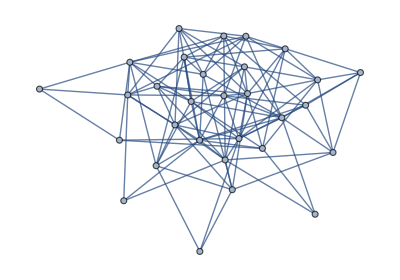

```mathematica
AdjacencyGraph[adj]
```

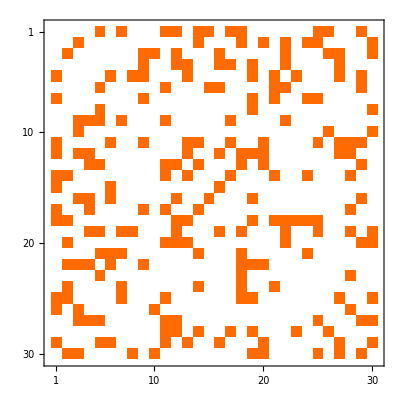

```mathematica
MatrixPlot[adj]
```

```mathematica
αstep:=α*δ;
βstep:=β*δ;
δ=0.5;
k=40;α=0.2;β=0.1;
```

```mathematica
UpdatePop[n_]:=(
newbirths = RandomVariate[BinomialDistribution[n,Max[{0,(αstep*(1-n/k))}]]];
newdeaths= RandomVariate[BinomialDistribution[n,βstep]];
n+newbirths-newdeaths)
```

```mathematica
d=0.05 (*probability of dispersal *);
e=0.051 (*patch extinction probability *);
```

```mathematica
metapopup[popsvar_]:=(
pops=popsvar;(*we need to be able to write to our pops variable, so copy from the input argument*)
emmigrants=Table[RandomVariate[BinomialDistribution[pops[[i]],d]],{i,1,npop}];(*Choose how many emmigrants to send out*)
pops=pops-emmigrants;(*Remove the emmigrants from their natal populations*)
extinct=Sort[RandomSample[Table[i,{i,1,npop}],RandomVariate[BinomialDistribution[npop,e]]]]; (*choose pops to go extinct*)
Do[pops[[extinct[[i]]]]=0,{i,1,Length[extinct]}];(*delete extinct pops*)
pops=migratepops[pops,emmigrants];
Do[pops[[i]]=UpdatePop[pops[[i]]],{i,1,npop}];
pops)
```

```mathematica
migratepops[popsvar_,emmvar_]:=(
pops=popsvar;
Table[
If[emmvar[[i]]>0,
disperseto=RandomVariate[MultinomialDistribution[emmvar[[i]],Table[1/Length[links[[i]]],{Length[links[[i]]]}]]];
Do[pops[[links[[i,j]]]]+=disperseto[[j]],{j,1,Length[links[[i]]]}]];,{i,1,npop}] ;
pops)
```

#### Do the sim

```mathematica
e=0.03;
```

```mathematica
pops=Table[RandomVariate[BinomialDistribution[60,.5]],{i,1,npop}];
```

```mathematica
tmax=1000;
popstab={};
out={};t=0;While[(Total[pops]>0) &&( t<tmax),pops=metapopup[pops];AppendTo[out,Total[pops]];
AppendTo[popstab,pops];t++]
```

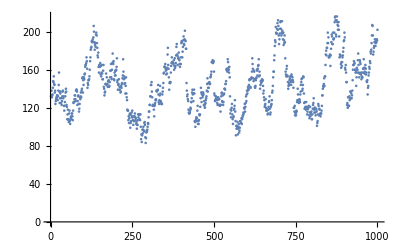

```mathematica
ListPlot[out]
```

```mathematica
daplots=Table[AdjacencyGraph[adj,VertexSize->Table[i-> popstab[[t,i]]/30,{i,1,npop}]],{t,1,1000}];
```

```mathematica
ListAnimate[daplots]
```

```mathematica
degrees=DegreeCentrality[AdjacencyGraph[adj]]/11;
```

```mathematica
closenesses=ClosenessCentrality[AdjacencyGraph[adj]];
```

```mathematica
eigenesses=EigenvectorCentrality[AdjacencyGraph[adj]];
```

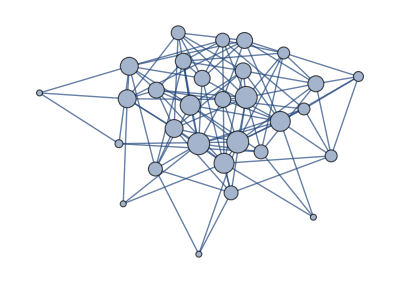

```mathematica
AdjacencyGraph[adj,VertexSize->Table[i->degrees[[i]],{i,1,npop}]]
```

```mathematica
curclose[pops_]:=Sum[pops[[i]]*closenesses[[i]],{i,1,npop}]/Total[pops]
```

```mathematica
curdeg[pops_]:=Sum[pops[[i]]*degrees[[i]],{i,1,npop}]/Total[pops]
```

```mathematica
cureig[pops_]:=Sum[pops[[i]]*eigenesses[[i]],{i,1,npop}]/Total[pops]
```

```mathematica
{Mean[closenesses],Mean[degrees]}//N
```

{0.539496,0.666667}

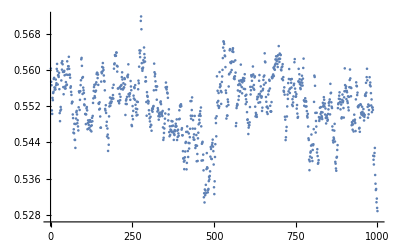

```mathematica
ListPlot[Table[tmp=popstab[[t]];curclose[tmp],{t,1,1000}]]
```

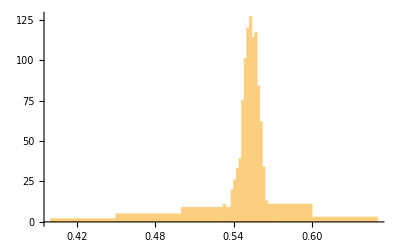

```mathematica
Show[Histogram[closenesses],Histogram[Table[tmp=popstab[[t]];curclose[tmp],{t,1,1000}]]]
```

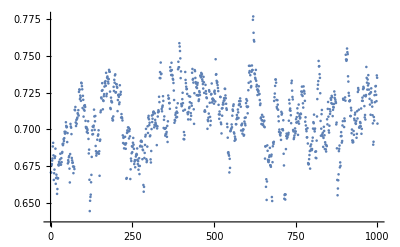

```mathematica
ListPlot[Table[tmp=popstab[[t]];curdeg[tmp],{t,1,1000}]]
```

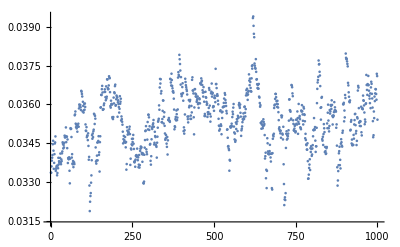

```mathematica
ListPlot[Table[tmp=popstab[[t]];cureig[tmp],{t,1,1000}]]
```